# Single-Electron Energy Levels of Heteronuclear Diatomic Molecules

```mathematica
SetDirectory[NotebookDirectory[]];
<<diatomic_base.m;
```

```mathematica
(* relative nuclear charge difference *)
ΔZrelval=(5-4)/((5+4)/2)
```

2/9

## Calculate single-electron energies in dependence of Z R

```mathematica
CalculatePlist[{l_,m_},pstart_,ZR_List,ΔZrel_]:=Module[{p0=pstart},{#,p0=CalculateP[{l,m},p0,{2,ΔZrel}#]}&/@ZR]
```

```mathematica
ZRrange=Prepend[Exp[Range[Log[0.05],Log[32],0.1]],0];
```

```mathematica
(* n,l,m,pFitSlopeOffset,numRadCoeffs,color *)
paraInfo=ParaInfo[ΔZrelval];
```

```mathematica
colors={(*1sσ*)Blue,(*1pσ*)Purple,(*2sσ*)Green,(*2pσ*)Red,(*1dσ*)Black,(*1pπ*)Brown,(*1p(-π)*)Brown,(*1dπ*)Orange,(*1d(-π)*)Orange,(*1fσ*)Magenta,(*2pπ*)Darker[Yellow],(*2p(-π)*)Darker[Yellow],(*3sσ*)Gray};
```

```mathematica
{QuantNumbersToString[#⟦1;;3⟧],#⟦4,1⟧}&/@paraInfo
```

{{1sσ,0.555556},{1pσ,0.444444},{2sσ,0.277778},{2pσ,0.222222},{1dσ,0.277778},{1p(+π),0.277778},{1p(-π),0.277778},{1d(+π),0.222222},{1d(-π),0.222222},{1fσ,0.222222},{2p(+π),0.185185},{2p(-π),0.185185},{3sσ,0.185185}}

```mathematica
(* 2p(±π)_u 3 Subscript[sσ, g] 3 Subscript[pσ, u] 3p(±π)_u *)
```

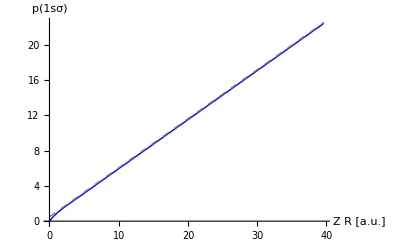

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

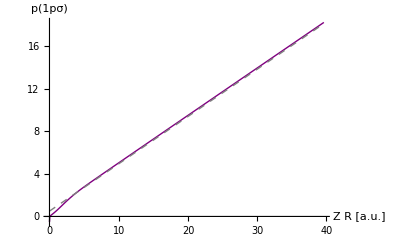

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

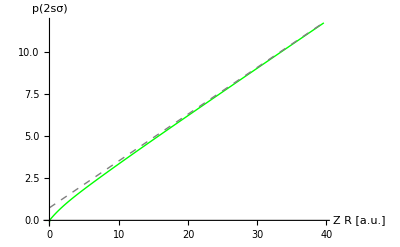

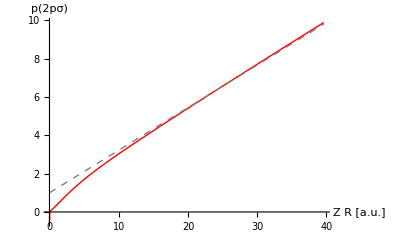

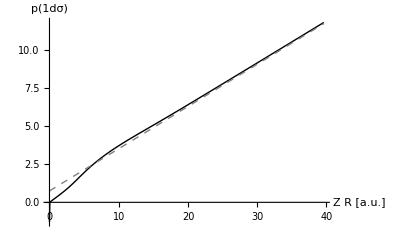

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

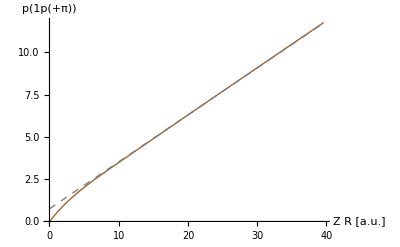

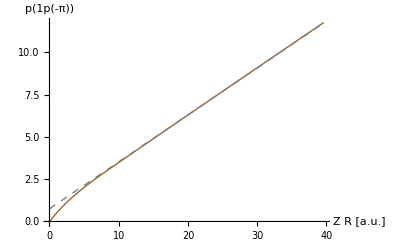

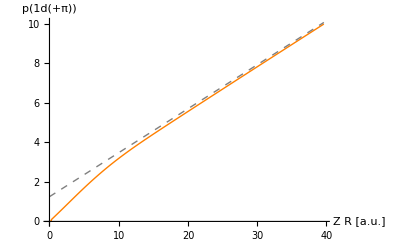

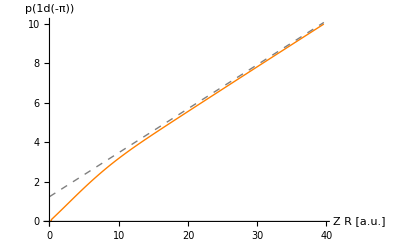

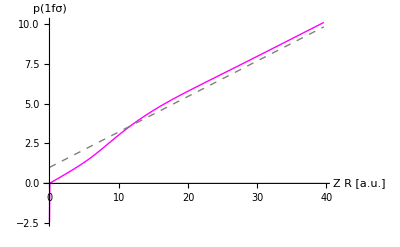

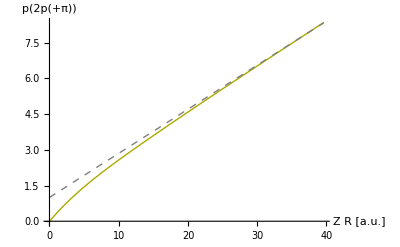

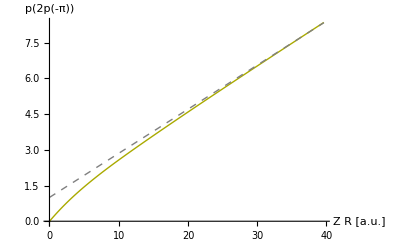

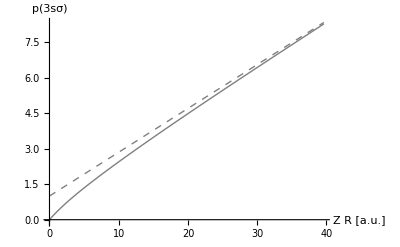

```mathematica
For[i=1,i≤Length[paraInfo],i++,
curInfo=paraInfo⟦i⟧;
Subscript[pPlot, i]=ListPlot[{CalculatePlist[{curInfo⟦2⟧,Abs[curInfo⟦3⟧]},curInfo⟦4,1⟧Max[ZRrange]+curInfo⟦4,2⟧,Reverse[ZRrange],ΔZrelval],{#,curInfo⟦4,1⟧#+curInfo⟦4,2⟧}&/@ZRrange},Joined->True,AxesLabel->{"Z R [a.u.]","p("<>QuantNumbersToString[curInfo⟦1;;3⟧]<>")"},PlotStyle->{colors⟦i⟧,{Gray,Dashed}}];
Print[Subscript[pPlot, i]];]
```

### Assemble plots

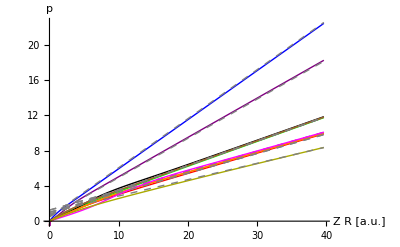

```mathematica
Show[Subscript[pPlot, #]&/@Range[Length[paraInfo]-2],AxesLabel->{"Z R [a.u.]","p"}]
```